# What's new in GTPack 1.1

GTPack version 1.1 was released on March 1st, 2020. Besides several bug fixes, GTPack 1.1 comes with a new sub package GTRepresentationTheorySG allowing for the calculation of representation matrices and character tables of space groups. It furthermore provides novel functionality for electronic structure calculations.

Handling and representation theory of space groups

GTPack 1.1 offers a few new modules to handle symmetry elements of space groups.

GTSGgmatpaclet:GroupTheory/ref/GTSGgmatGroupTheory Package Symbol | multiplies two space group elements
GTSGOrderOfElementpaclet:GroupTheory/ref/GTSGOrderOfElementGroupTheory Package Symbol | gives the order of a space group element

We will show the examples of this section for a monoclinic lattice.

```mathematica
Needs["GroupTheory`"]
```

```mathematica
basis= {{a,0,0},{0,b,0},{c Cos[β],0,c Sin[β]}}
```

{{a,0,0},{0,b,0},{c Cos[β],0,c Sin[β]}}

```mathematica
GTSGgmat[⟨C2y,{0,1/2,1/2}⟩,⟨IC2y,{0,1/2,1/2}⟩,basis]
```

⟨IEe,{0,0,0}⟩

```mathematica
GTSGOrderOfElement[⟨C2y,{0,1/2,1/2}⟩,basis]
```

2

Additionally, GTPack 1.1 provides several new modules to analyze the group structure of space groups..

GTSGClassespaclet:GroupTheory/ref/GTSGClassesGroupTheory Package Symbol | multiplies two space group elements
GTSGGetInvSubGrouppaclet:GroupTheory/ref/GTSGGetInvSubGroupGroupTheory Package Symbol | gives the order of a space group element
GTSGLeftCosetspaclet:GroupTheory/ref/GTSGLeftCosetsGroupTheory Package Symbol | gives the left cosets of the factor group G/T (G being a space group, T the group of pure lattice translations) with respect to a subgroup
GTSGRightCosetspaclet:GroupTheory/ref/GTSGRightCosetsGroupTheory Package Symbol | gives the right cosets of the factor group G/T (G being a space group, T the group of pure lattice translations) with respect to a subgroup
GTSGCosetRepresentativepaclet:GroupTheory/ref/GTSGCosetRepresentativeGroupTheory Package Symbol | determines a coset representative for a left coset decomposition of the factor group G/T (G being a space group, T the group of pure lattice translations) into a normal subgroup of index 2 or 3

We choose the monoclinic space group P2_1/c (#14). We calculate the corresponding basis vectors of the reciprocal lattice using GTReciprocalBasispaclet:GroupTheory/ref/GTReciprocalBasisGroupTheory Package Symbol. Then we install the space groups using GTInstallGrouppaclet:GroupTheory/ref/GTInstallGroupGroupTheory Package Symbol.

```mathematica
recbas=GTReciprocalBasis[basis]
```

{{(2 π)/a,0,-(2 π Cot[β])/a},{0,(2 π)/b,0},{0,0,(2 π Csc[β])/c}}

```mathematica
grp=GTInstallGroup[14]
```

{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

```mathematica
classes=GTSGClasses[grp,basis]
```

{{⟨Ee,{0,0,0}⟩},{⟨(IC^)_(2y)^,{0,1/2,1/2}⟩},{⟨IEe,{0,0,0}⟩},{⟨(C^)_(2y)^,{0,1/2,1/2}⟩}}

```mathematica
invsg=GTSGGetInvSubGroup[grp,classes,basis,2]
```

{⟨Ee,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

We can use a coset representative to reconstruct a space group from an invariant subgroup.

```mathematica
{qel,perm}=GTSGCosetRepresentative[grp,invsg,basis]
```

{⟨(C^)_(2y)^,{0,1/2,1/2}⟩,Cycles[{{2,4,3}}]}

```mathematica
generate=invsg;
Do[generate=Append[generate,GTSGgmat[qel,invsg[[i]],basis]],{i,1,Length[invsg]}]
```

```mathematica
generate
```

{⟨Ee,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩}

```mathematica
grp
```

{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

```mathematica
Permute[generate,perm]
```

{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

Finally, we calculate the left and right cosets, which are identical for an invariant subgroup.

```mathematica
GTSGLeftCosets[grp,invsg,basis]
```

{{⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩},{⟨Ee,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}}

```mathematica
GTSGRightCosets[grp,invsg,basis]
```

{{⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩},{⟨Ee,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}}

The probably most important modules for space groups which were introduced in GTPack 1.1 concern the calculation of the irreducible representations and character table of space groups.

GTSGCharacterTablepaclet:GroupTheory/ref/GTSGCharacterTableGroupTheory Package Symbol | gives the character table of a space group
GTSGGetIrepspaclet:GroupTheory/ref/GTSGGetIrepsGroupTheory Package Symbol | gives the character table and representation matrices of a space group

```mathematica
{classes,characters,names}=GTSGCharacterTable[grp,{0,1/2,0},recbas]
```

Classes of G/T:

C_1 = {⟨Ee,{0,0,0}⟩}

C_2 = {⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

C_3 = {⟨IEe,{0,0,0}⟩}

C_4 = {⟨(C^)_(2y)^,{0,1/2,1/2}⟩}

| ⟨Ee,{0,0,0}⟩ | ⟨(IC^)_(2y)^,{0,1/2,1/2}⟩ | ⟨IEe,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | 2 | 0 | 0 | 0

{{{⟨Ee,{0,0,0}⟩},{⟨(IC^)_(2y)^,{0,1/2,1/2}⟩},{⟨IEe,{0,0,0}⟩},{⟨(C^)_(2y)^,{0,1/2,1/2}⟩}},{{2,0,0,0}},{Γ^1}}

```mathematica
{{classes,characters,names},{groupofk,irepsofk},{fullgroup,ireps}}=GTSGGetIreps[grp,{0,1/2,0},recbas];
```

Specified k-vector (Cartesian): {0,π/b,0}

Specified k-vector (Direct)   : {0,1/2,0}

Group of the k-vector:

{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

Star of the k-vector: (1 arm)

{{0,π/b,0}}

Representation matrices of the group of k:

| ⟨Ee,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩ | ⟨IEe,{0,0,0}⟩ | ⟨(IC^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | (1 | 0
0 | 1) | (0 | 1
-1 | 0) | (-1 | 0
0 | 1) | (0 | 1
1 | 0)

Representation matrices of the space group:

| ⟨Ee,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩ | ⟨IEe,{0,0,0}⟩ | ⟨(IC^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | (1 | 0
0 | 1) | (0 | 1
-1 | 0) | (1 | 0
0 | -1) | (0 | -1
-1 | 0)

Classes of G/T:

C_1 = {⟨Ee,{0,0,0}⟩}

C_2 = {⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

C_3 = {⟨IEe,{0,0,0}⟩}

C_4 = {⟨(C^)_(2y)^,{0,1/2,1/2}⟩}

| ⟨Ee,{0,0,0}⟩ | ⟨(IC^)_(2y)^,{0,1/2,1/2}⟩ | ⟨IEe,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | 2 | 0 | 0 | 0

```mathematica
{{classes,characters,names},{groupofk,irepsofk},{fullgroup,ireps}}=GTSGGetIreps[grp,{0,1/4,0},recbas]
```

Specified k-vector (Cartesian): {0,π/(2 b),0}

Specified k-vector (Direct)   : {0,1/4,0}

Group of the k-vector:

{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩}

Star of the k-vector: (2 arms)

{{0,π/(2 b),0},{0,(3 π)/(2 b),0}}

Representation matrices of the group of k:

| ⟨Ee,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | (1) | (-(-1)^(3/4))
Γ^2 | (1) | ((-1)^(3/4))

Representation matrices of the space group:

| ⟨Ee,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩ | ⟨IEe,{0,0,0}⟩ | ⟨(IC^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | (1 | 0
0 | 1) | (-(-1)^(3/4) | 0
0 | (-1)^(1/4)) | (0 | ⅈ
-ⅈ | 0) | (0 | (-1)^(1/4)
-(-1)^(3/4) | 0)
Γ^2 | (1 | 0
0 | 1) | ((-1)^(3/4) | 0
0 | -(-1)^(1/4)) | (0 | ⅈ
-ⅈ | 0) | (0 | -(-1)^(1/4)
(-1)^(3/4) | 0)

Classes of G/T:

C_1 = {⟨Ee,{0,0,0}⟩}

C_2 = {⟨(IC^)_(2y)^,{0,1/2,1/2}⟩}

C_3 = {⟨IEe,{0,0,0}⟩}

C_4 = {⟨(C^)_(2y)^,{0,1/2,1/2}⟩}

| ⟨Ee,{0,0,0}⟩ | ⟨(IC^)_(2y)^,{0,1/2,1/2}⟩ | ⟨IEe,{0,0,0}⟩ | ⟨(C^)_(2y)^,{0,1/2,1/2}⟩
Γ^1 | 2 | 0 | 0 | √2
Γ^2 | 2 | 0 | 0 | -√2

{{{{⟨Ee,{0,0,0}⟩},{⟨(IC^)_(2y)^,{0,1/2,1/2}⟩},{⟨IEe,{0,0,0}⟩},{⟨(C^)_(2y)^,{0,1/2,1/2}⟩}},{{2,0,0,√2},{2,0,0,-√2}},{Γ^1,Γ^2}},{{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩},{{{{1}},{{-(-1)^(3/4)}}},{{{1}},{{(-1)^(3/4)}}}}},{{⟨Ee,{0,0,0}⟩,⟨(C^)_(2y)^,{0,1/2,1/2}⟩,⟨IEe,{0,0,0}⟩,⟨(IC^)_(2y)^,{0,1/2,1/2}⟩},{{{{1,0},{0,1}},{{-(-1)^(3/4),0},{0,(-1)^(1/4)}},{{0,ⅈ},{-ⅈ,0}},{{0,(-1)^(1/4)},{-(-1)^(3/4),0}}},{{{1,0},{0,1}},{{(-1)^(3/4),0},{0,-(-1)^(1/4)}},{{0,ⅈ},{-ⅈ,0}},{{0,-(-1)^(1/4)},{(-1)^(3/4),0}}}}}}

Exploring orbital characters in electronic structure calculations

GTPack 1.1 offers a new functionality to highlight the orbital character in electronic structure calculations.

GTPartialDOSpaclet:GroupTheory/ref/GTPartialDOSGroupTheory Package Symbol | calculation of partial densities of states (TB Hamiltonians)
GTFatBandsPlotpaclet:GroupTheory/ref/GTFatBandsPlotGroupTheory Package Symbol | plots orbital character of a band structure (TB Hamiltonians)

We show the new modules on the example of Cu. The corresponding data is loaded from an existing dataset. Furthermore, we generate a high-symmetry path for the fcc lattice using GTBZPathpaclet:GroupTheory/ref/GTBZPathGroupTheory Package Symbol and the corresponding k-mesh using GTBZLinespaclet:GroupTheory/ref/GTBZLinesGroupTheory Package Symbol.

```mathematica
SetDirectory[NotebookDirectory[]<>"../ReferencePages/Symbols/datasets"];
hfcc= GTReadFromFile["fcc_spd.ham"];
cu=GTTbDatabaseRetrieve["TB_parametersets/TB_Handbook","Cu"];
hfccp=hfcc /. GTTbParmToRule[cu];

kp=GTBZPath["fcc"];
kpl=GTBZLines[kp,{10,10,10,10,10,10}];
```

To calculate fat bands the eigenvectors of the Hamiltonian are needed, which can be calculated using GTBandspaclet:GroupTheory/ref/GTBandsGroupTheory Package Symbol.

```mathematica
bands=GTBands[hfccp,kpl,9,GOVerbose->False,GOEigenvectors->True];
```

Maximum Abscissa = 4.48735

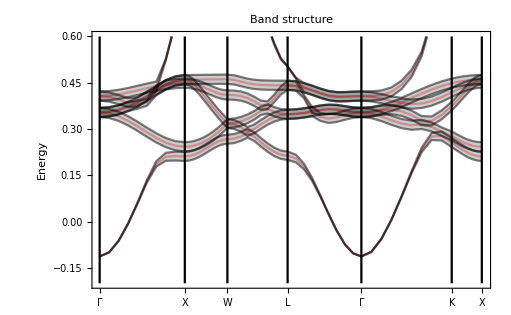

```mathematica
GTFatBandsPlot[bands,9,0.03,PlotRange->{{0,4.5},{-.2,.6}},Joined->True,GOFatBands->{"d",{5,6,7,8,9}},PlotStyle->Black]
```

Using the novel module GTPartialDOSpaclet:GroupTheory/ref/GTPartialDOSGroupTheory Package Symbol we can also obtain the density of states for specified orbitals. For the partial DOS calculation, we provide a parameter list, where the last item describes which partial densities of states are calculated.

```mathematica
dosp={5,1,-.2,1.2,501,0.,1,{{"e_g",{7,9}},{"t_(2  g)",{5,6,8}}}};
```

916 k-points calculated

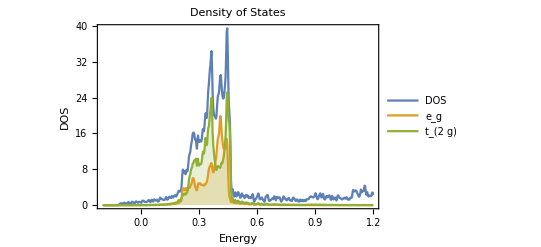

```mathematica
GTPartialDOS[hfccp,"fcc",dosp,GOPlotDos->"PDOS"]
```

Further modifications

Besides the new modules presented above, some existing modules where extended. For GTClusterManipulatepaclet:GroupTheory/ref/GTClusterManipulateGroupTheory Package Symbol, the new method "Impurities" was added, which allows to substitute a randomly chosen selection of one atomic species within a cluster by impurities. GTDensityOfStatesRSpaclet:GroupTheory/ref/GTDensityOfStatesRSGroupTheory Package Symbol was extended to allow for eigenvalues of an electronic structure calculation as an input. This way, computationally demanding eigenvalue problems can be solved outside of Mathematica.

| Related Guides
▪W. Hergert, R. M. Geilhufe, Group Theory in Solid State Physics and Photonics: Problem Solving with Mathematica, Wiley-VCH, ISBN: 978-3-527-41133-7 (2018).http://gtpack.org/book/